# Code

```mathematica
importALPSGenes[filename_]:=Select[Import[filename,"Table"], Length[#] == geneCount&]
```

```mathematica
importALPSOut[filename_] := Select[Import[filename,"Table"], Length[#] == 3&]
```

```mathematica
importGenesFromRun[resultName_, expName_, runNo_] := Module[{file},
file= Last[FileNames[resultName <> "/" <> ToString[expName] <> "/" <> ToString[runNo] <> "-*.pop"]];
importALPSGenes[file]]
```

```mathematica
importResults[directoryName_] := Module[{files},
files = FileNames["*.out",{directoryName},2];
combineResults[Map[{FileBaseName[DirectoryName[#]] , importALPSOut[#]}&, files]]]
```

```mathematica
chartOfResults[directoryName_] := Module[{res},
res = importResults[directoryName];
BarChart[Map[Mean,values[res]], 
	ChartLegends -> keys[res], ChartStyle -> "DarkRainbow"]]
```

```mathematica
combineResultsHelper[splitResult_] := Module[{name, justData},
name = splitResult[[1,1]];
justData = Map[#[[2]]&, splitResult];
name ->  Map[#[[-1,-1]]&, justData]]
```

```mathematica
combineResults[results_] := Module[{},
Map[combineResultsHelper, SplitBy[results, #[[1]]&]]]
```

```mathematica
indexOfMinimum[fun_, inputs_] := Module[{outputs, min},
outputs = Map[fun, inputs];
min = Min[outputs];
Flatten[Position[outputs, min]]]
```

```mathematica
indexOfMaximum[fun_, inputs_] := Module[{outputs, min},
outputs = Map[fun, inputs];
min = Max[outputs];
Flatten[Position[outputs, min]]]
```

```mathematica
importMinGene[filename_, fitnessForGene_] := Module[{genes, index,  indexes},
genes = importALPSGenes[filename];
indexes = indexOfMinimum[fitnessForGene, genes];
If[Length[indexes] > 1,
Message[importBestGenes::notuniq]];
index = First[indexes];
genes[[index]]]
```

```mathematica
importMaxGene[filename_, fitnessForGene_] := Module[{genes, index,  indexes},
genes = importALPSGenes[filename];
indexes = indexOfMaximum[fitnessForGene, genes];
If[Length[indexes] > 1,
Message[importBestGenes::notuniq]];
index = First[indexes];
genes[[index]]]
```

# Read Results

```mathematica
target = {0, 0.1}
```

{0,0.1}

```mathematica
fitness = fitnessToTarget[#, target, Ao, 1]&;
fitnessData = fitnessToTargetData[#, target, Ao, 1]&;
```

```mathematica
fitness = fitnessToTarget[#, target, Ap, 1]&;
fitnessData = fitnessToTargetData[#, target, Ap, 1]&;
```

```mathematica
fitness = fitnessForSpeed[#, Bp, 1]&;
fitnessData = fitnessForSpeedData[#, Bp, 1]&;
```

```mathematica
fitness = fitnessForSpeed[#, Ap, 1]&;
fitnessData = fitnessForSpeedData[#, Ap, 1]&;
```

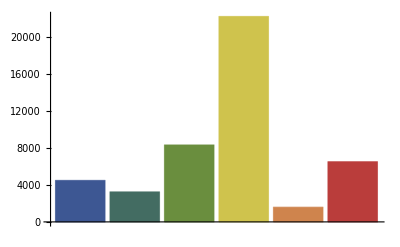
-Graphics--Graphics- | 0
-Graphics- | 1
-Graphics- | Ao
-Graphics- | Ap
-Graphics- | Bo
-Graphics- | Bp

```mathematica
chartOfResults["res1"]
```

```mathematica
target = {0,1} .4 m //. params
```

{0.,0.4}

```mathematica
RK4StepSize = 0.02;
```

```mathematica
target = {0,1} 0.2
```

{0.,0.2}

```mathematica
gene = importBestGenes["speed-BAD-1.pop", fitness];
```

importBestGenes::notuniq: -- Message text not found --

```mathematica
fitness[gene]
```

666.6

```mathematica
RK4StepSize = 0.01;
```

```mathematica
fitness[gene]
```

1.49617

```mathematica
data = fitnessData[gene];
```

```mathematica
(* ran a mean speed test got: 1.30e-03 as the max after 16k evaluations. *)
```

```mathematica
link = Install["9", LinkMode-> Connect]
```

LinkObject[9,8895,8]

```mathematica
Uninstall[link]
```

9

```mathematica
runSimulationMlink[{0}~Join~Table[0., {stateCount - 1}], 0.01, Table[.5, {constantsCount}],10.]
```

{10.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.07107,0.}

```mathematica
NestList[runSimulationMlink[#, 0.01, Table[.5, {constantsCount}],0.1]&, {0}~Join~Table[0., {stateCount - 1}], 10]
```

```mathematica
NestList[runSimulationMlink[#, 0.01, Table[.5, {constantsCount}],0.1]&, {0}~Join~Table[0., {stateCount - 1}], 10]
```

```mathematica
NestList[runSimulationMlink[#, 0.01, Table[.5, {constantsCount}],0.1]&, {0}~Join~Table[0., {stateCount - 1}], 10]
```

```mathematica
NestList[runSimulation[#, 0.01, Table[.5, {constantsCount}],0.1]&, {0}~Join~Table[0., {stateCount - 1}], 10]
```

```mathematica
gene = initGene[];
```

```mathematica
fitness[gene]
```

1.43755

```mathematica
Block[{runSimulationGA = runSimulation}, fitness[gene]]
```

1.6554

```mathematica
Block[{runSimulationGA = runSimulationMlink}, fitness[gene]]
```

1.43755

```mathematica
Timing[data = Block[{runSimulationGA = runSimulationMlink}, fitnessData[gene]];]
```

{0.01427,Null}

```mathematica
Timing[data2 = fitnessData[gene];]
```

{0.013954,Null}

```mathematica
processCollision[Array[s,stateCount]] /. s[a_] -> s[a - 1]
```

{s[0],s[1],s[2],s[3],s[4],s[5],s[6],s[7],s[8],s[9],s[10],s[11],If[(s[4]>π/2&&s[12]>0)||(s[4]<-π/2&&s[12]<0),-0.8,1] s[12],If[(s[5]>π/2&&s[13]>0)||(s[5]<-π/2&&s[13]<0),-0.8,1] s[13],If[(s[6]>π/2&&s[14]>0)||(s[6]<-π/2&&s[14]<0),-0.8,1] s[14],If[(s[7]>π/2&&s[15]>0)||(s[7]<-π/2&&s[15]<0),-0.8,1] s[15],If[(s[8]>π/2&&s[16]>0)||(s[8]<-π/2&&s[16]<0),-0.8,1] s[16],s[17],s[18],s[19],s[20],s[21],s[22],s[23],s[24],s[25]}